```mathematica
grContPl0=ContourPlot3D[y^2*z^2+z^2*x^2+x^2*y^2+2*x*y*z==0,{x,-1,1},{y,-1,1},{z,-1,1},AxesLabel->{x,y,z},Mesh->5,ViewPoint->{3.2,0.9,0.8},ImageSize->300,MaxRecursion->5];
grContPl1=ContourPlot3D[y^2*z^2+z^2*x^2+x^2*y^2+2*x*y*z==0,{x,-1,1},{y,-1,1},{z,-1,1},Mesh->5,ColorFunction->Function[{x,y,z,f},Evaluate[Hue[z]]],MaxRecursion->5,AxesLabel->{x,y,z},ViewPoint->{3.2,0.9,0.8},ImageSize->300];
Row[{grContPl0,grContPl1},Spacer[20]]
```

-Graphics3D--Graphics3D-

```mathematica
Print[Style[Text["Человек-яйцо"],FontSize->22,FontFamily->"Algerian",FontColor->Magenta]];
Show[ParametricPlot3D[(1-0.25 Cos[u]) {Sin[u] Cos[v],Sin[u] Sin[v],0}+{0,0,1.05 Cos[u]},{u,0,Pi},{v,0,2 Pi},MeshFunctions->{Function[{x,y,z,u,v},x+0.5 (2 y^2-2 (z+0.5))^2]},MeshShading->{Black,Lighter@Red,Yellow},Mesh->{{-0.85,-0.82}},AxesLabel->{"x","y","z"},PlotPoints->100],ParametricPlot3D[Sin[1.9 (u-0.45)]^2 (0.36+0.8 (Sqrt[0.5+2 Abs[v]])) Cos[1.5 v]*{-Sin[u] Cos[v],-Sin[u] Sin[v],Cos[u]},{u,Pi/6,Pi/2},{v,-Pi/6,Pi/6},MeshFunctions->{Function[{x,y,z,u,v},Sin[1.9 (u-0.49)]^2 (0.36+0.8 (Sqrt[0.5+2 Abs[v]])) Cos[1.5 v]]},MeshShading->{White,Lighter@Blue,Black},Mesh->{{1.06,1.077}},AxesLabel->{"x","y","z"},PlotPoints->100],ParametricPlot3D[{-1.1*u,0,-u^2/4-0.15}+0.35 Sqrt[Sqrt[(1.21-u)]]*(2 Cos[v] {0,1,0} +0.7*Sin[v] {-u/2,0,1-0.5 Sin[v]}/Sqrt[u^2+1]),{u,0.5,1.2},{v,0,2 Pi},PlotStyle->LightBrown,Mesh->None],PlotRange->All,ViewPoint->{-3,-1.3,0.8},ImageSize->450]
```

Человек-яйцо

-Graphics3D-

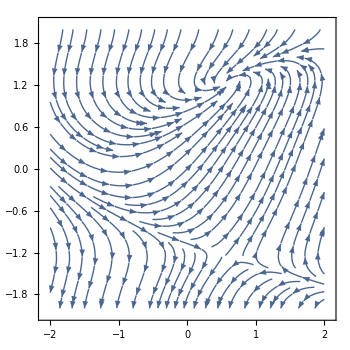
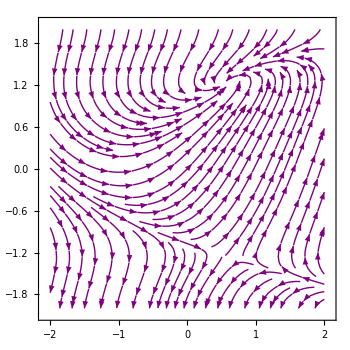

```mathematica
vctFld={Cos[y^2],1+x-y^2};
grVect1=StreamPlot[vctFld,{x,-2,2},{y,-2,2},ImageSize->350];
grVect2=StreamPlot[vctFld,{x,-2,2},{y,-2,2},ImageSize->350,StreamStyle->Purple];
Row[{grVect1,grVect2},Spacer[20]]
```

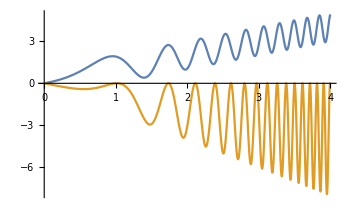
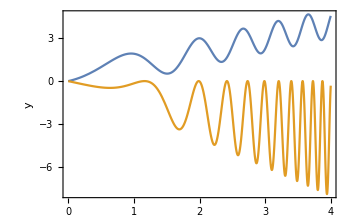

```mathematica
xFrmLbl="x(cm)";
yFrmLbl="f1,f2";
grf1=Plot[{x+Sin[2*x^2.5],x*Sin[1.5*x^3]-x},{x,0,4.},BaseStyle->18,ImageSize->350];
grf2=Plot[{x+Sin[2*x^2],x*Sin[x^3]-x},{x,0,4},BaseStyle->18,ImageSize->350,Frame->True,FrameLabel->{None,y,xFrmLbl,yFrmLbl}];
Row[{grf1,grf2},Spacer[15]]
```

```mathematica
StringLength["Frame→True,FrameLabel→{None,y,xFrmLbl,yFrmLbl}"]
(*уточнить*)
```

46

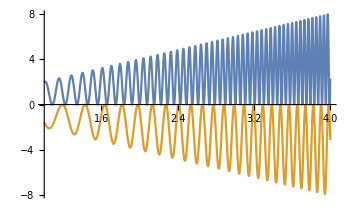
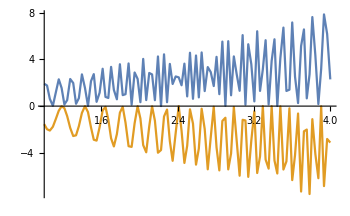

```mathematica
grf1=Plot[{x+x*Sin[20*x^2],x*Sin[10*x^2]-x},{x,1,4},BaseStyle->15,ImageSize->350];
grf2=Plot[{x+x*Sin[20*x^2],x*Sin[10*x^2]-x},{x,1,4},BaseStyle->15,ImageSize->350,MaxRecursion->1];
Row[{grf1,grf2},Spacer[15]]
```